```mathematica
(*Ako ˇzelite da ogradite parcelu u obliku pravougaonika dimenzija 150m×85m,a znamo
da je greˇska prilikom merenja ne ve ́ca od 6cm,na ́ci pribliˇznu vrednost povrˇsine ove parcele
i granicu apsolutne i relativne greˇske.*)
```

```mathematica
p=150*85
```

12750

```mathematica
pmax=(150+0.06)*(86+0.06)
```

12914.2

```mathematica
pmin=(150-0.06)*(86-0.06)
```

12885.8

```mathematica
ag=Abs[Max[pmax,pmin]-p]
```

164.164

```mathematica
rg=ag/Abs[p]
```

0.0128756

```mathematica
(*Na ́ci Lagranˇzov oblik interpolacionog polinoma,koji interpolira ove podatke.*)
```

```mathematica
cv={{8,123},{11,137},{13,142},{16,153},{22,151}}
```

{{8,123},{11,137},{13,142},{16,153},{22,151}}

```mathematica
lag[cv_,x_]:=Module[{},
m=Length[cv];
w=1;
pol=0;
Do[
w=w*(x-cv[[i,1]]),
{i,1,m}];
Do[
wi=w/(x-cv[[i,1]]);
pol=pol+cv[[i,2]]*wi/(wi/.x->cv[[i,1]]),
{i,1,m}];
pol
]
```

```mathematica
lagpol[x_]=lag[cv,x];
```

```mathematica
s=lagpol[14]//N
```

145.073

```mathematica
tac=147;
```

```mathematica
ag=Abs[s-tac]
```

1.92727

```mathematica
rg=ag/Abs[tac]
```

0.0131107

```mathematica
(*Na ́ci linearni splajn koji interpolira ove podatke.*)
```

```mathematica
splajn=Interpolation[cv,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
lins=splajn[14]//N
```

145.667

```mathematica
ag1=Abs[tac-lins]
```

1.33333

```mathematica
rg1=ag1/Abs[tac]
```

0.00907029

```mathematica
cv={{1984,9.99},{1988,9.92},{1996,9.84},{2004,9.85},{2008,9.69},{2016,9.81}}
```

{{1984,9.99},{1988,9.92},{1996,9.84},{2004,9.85},{2008,9.69},{2016,9.81}}

```mathematica
nk=Fit[cv,{1,t,t^2},t]
```

1359.31-1.3432 t+0.000334226 t^2

```mathematica
gr1=ListPlot[cv];
```

```mathematica
gr2=Plot[nk,{t,1984,2016}];
```

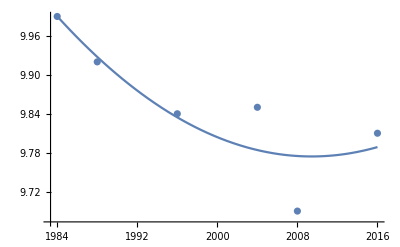

```mathematica
Show[gr1,gr2]
```

```mathematica
(*Napisati program koji za zadati skup od n+1 ˇcvorova kreira interpolacioni polinom
n-tog stepena u obliku p(x)=a0+a1(x+2)+a2(x+2)2+ . . .+an(x+2)n i testirati ga 
na problemu iz tre ́ceg zadatka.*)
```

```mathematica
zad4[cv_,x_]:=Module[{},
m=Length[cv];
a=Table[1,{i,1,m},{j,1,m}];
Do[
a[[i,j]]=(cv[[i,1]]+2)^(j-1),
{i,1,m},{j,2,m}];
b=Table[cv[[i,2]],{i,1,m}];
koef=LinearSolve[a,b];
baza=Table[(x+2)^i,{i,0,m-1}];
koef.baza
]
```

```mathematica
cv={{1984,9.99},{1988,9.92},{1996,9.84},{2004,9.85},{2008,9.69},{2016,9.81}}
```

{{1984,9.99},{1988,9.92},{1996,9.84},{2004,9.85},{2008,9.69},{2016,9.81}}

```mathematica
p[x_]=zad4[cv,x]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,1986.,3.9442×10^6,7.83317×10^9,1.55567×10^13,3.08956×10^16},{1.,1990.,3.9601×10^6,7.8806×10^9,1.56824×10^13,3.1208×10^16},{1.,1998.,3.992×10^6,7.97602×10^9,1.59361×10^13,3.18403×10^16},{1.,2006.,4.02404×10^6,8.07222×10^9,1.61929×10^13,3.24829×10^16},{1.,2010.,4.0401×10^6,8.1206×10^9,1.63224×10^13,3.2808×10^16},{1.,2018.,4.07232×10^6,8.21795×10^9,1.65838×10^13,3.34662×10^16}} may contain significant numerical errors.

-3.04914×10^10+7.62371×10^7 (2+x)-76245. (2+x)^2+38.1262 (2+x)^3-0.00953237 (2+x)^4+9.53311×10^-7 (2+x)^5

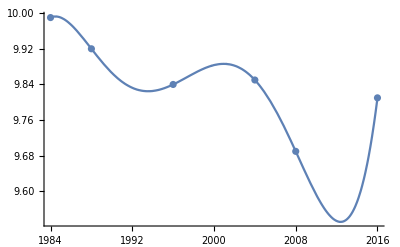

```mathematica
Show[ListPlot[cv], Plot[p[x],{x,1984,2016}],PlotRange->All]
```